# Universal Estimator

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

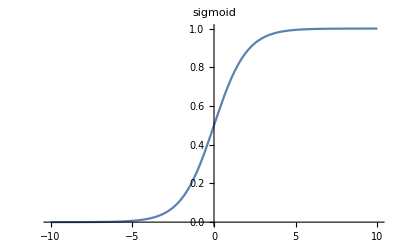

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
Plot[Sigmoid[x], {x, -10, +10}, PlotLabel->HoldForm[sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

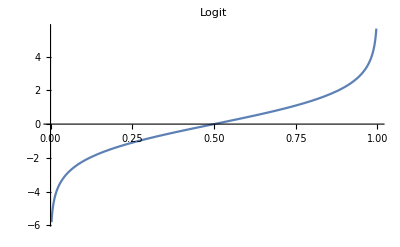

```mathematica
Logit[x_]:= Log[x/(1-x)]
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

We define an Adjuster function which returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.
We can use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

### Test Adjuster

For example, we can create an Adjuster for the range [2,5] and call it with values ∈ [0,1]

```mathematica
adj=Adjuster[2, 5];
Print[adj[0.01]];
```

2.01076

```mathematica
Print[adj[0.99]];
```

4.84348

Plot of the adjuster output in the range [0,1]

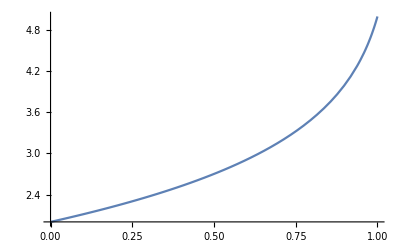

```mathematica
Print[Plot[adj[x], {x,0,1}]]
```

## Generate data

Arguments:

nSamples: number of samples

M: number of observations in each sample

f: the function to generate samples

ranges: an array [d X 2] of parameter ranges (e.g. for 2 parameters: [[0, 10], [0, ∞]])

bins: number of bins in histograms (default: max[samples]+1)

Returns:

a table of associations: histogram -> params (over all samples)

```mathematica
GenerateData[nSamples_, M_, f_, ranges_, bins_:-1]:= 
Module[{nParams, adjusters, params, samples, nbins, histograms},

(*number of parameters*)
nParams=Dimensions[ranges][[1]];

(*generate an adapter for each parameter range*)
adjusters=Table[Adjuster[ranges[[i,1]],ranges[[i,2]]],{i,1,nParams}];

(*generate N parameters cube in the range (0,1)*)
params=Table[adjusters[[j]][RandomReal[{0,1}]],{i,1,nSamples},{j,1,nParams}];

(*generate N samples from the parameters*)
samples=Table[f[params[[i]],M],{i,1,nSamples}];

(*create a histogram from each sample*)
nbins=If [bins>0,bins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];

(*output*)
Table[h@samples[[i]]-> params[[i]], {i, 1, nSamples}]
]
```

Test GenerateData

```mathematica
YuleSimon[{alpha_,beta_}, size_]:=RandomVariate[WaringYuleDistribution[alpha,beta],size];
YuleSimonRanges = {{2,3},{0,10}};

data = GenerateData[5,10,YuleSimon, YuleSimonRanges];
Print[data//TableForm]
```

{5,3,2,0,0,0}→{2.6006,3.40591}
{10,0,0,0,0,0}→{2.12397,0.969408}
{9,0,0,1,0,0}→{2.39451,1.00211}
{7,1,2,0,0,0}→{2.44179,1.94835}
{7,0,2,0,0,1}→{2.08345,0.400935}

## DNN

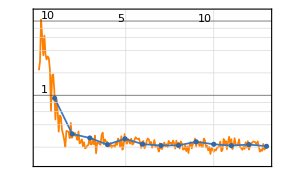
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:208  rounds:13  time:23s  examples/s:590
data | ,,  training examples:1000  validation examples:250  processed examples:13312  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.09×10^-1
validation | ,,  loss:2.05×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
CreateNet[bins_, nParams_]:=( 
NetChain[{
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp],
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp],
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[nParams]},
"Input"->bins, 
"Output" -> nParams]
)

M = 256;
nSamples = 1000;
trainSet=GenerateData[nSamples,M,YuleSimon, YuleSimonRanges];
bins = Length@trainSet[[1]][[1]];
valSet=GenerateData[nSamples/4,M,YuleSimon, YuleSimonRanges, bins];
nParams=Dimensions[YuleSimonRanges][[1]];
net = NetInitialize@CreateNet[bins, nParams];
(*Print[NetGraph[net]];*)
trained=NetTrain[net,trainSet,All, Method->"ADAM", 
ValidationSet->valSet, 
LossFunction->MeanAbsoluteLossLayer[]];
trained
```

## Experiments

```mathematica
(*results = Import["/home/yossi/Documents/Wolfram Mathematica/cached_mesh_points.csv"];
Print[results//TableForm];*)

(*dict["sample"] = YuleSimon
dict["ranges"] = {{2,3},{0,10}}
dict["M"] = 256
f = dict["sample"]
ranges = dict["ranges"]
f[ranges[[1,1]], dict["M"]]
*)
```